```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]<>"\\MethodsODE\\OutputData\\"];

(* Модуль для создания фазовой плоскости *)
PlotFaze[ data_]  := Module[{point, plot},
point = Table[Table[{data[[n]][[i]], data[[n+1]][[i]]}, {i, 1, Length[data[[1]]]}], {n, 1, Length[data]-1, 2}];

plot = ListPlot[point,ImageSize->800,  AxesLabel->{"u1", "u2"}, AxesStyle->Arrowheads[0.03], PlotRange->{{-2, 2}, {-2, 2}}, Frame -> True, Joined -> True];

Show[plot]
]
```

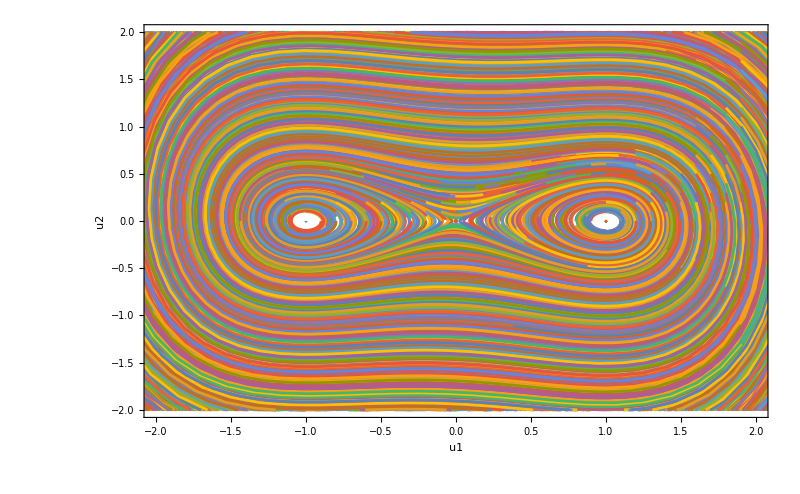

```mathematica
data1 = Import["FZ1", "Table"];
PlotFaze[data1]
```

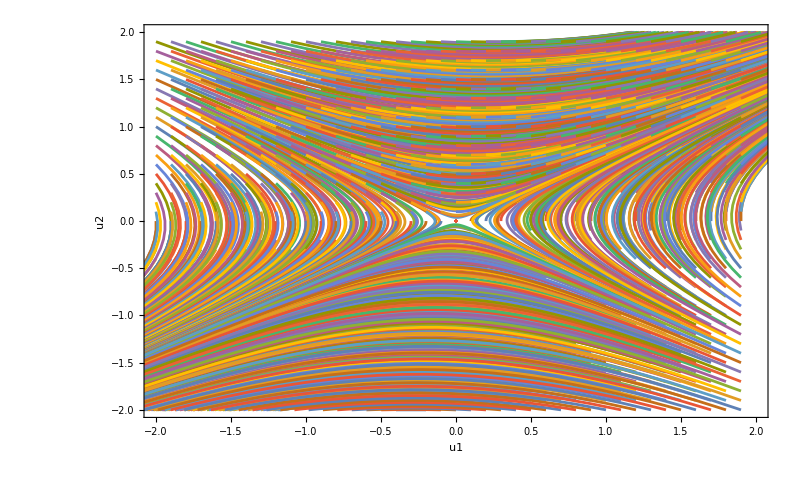

```mathematica
data2 = Import["FZ2", "Table"];
PlotFaze[data2]
```

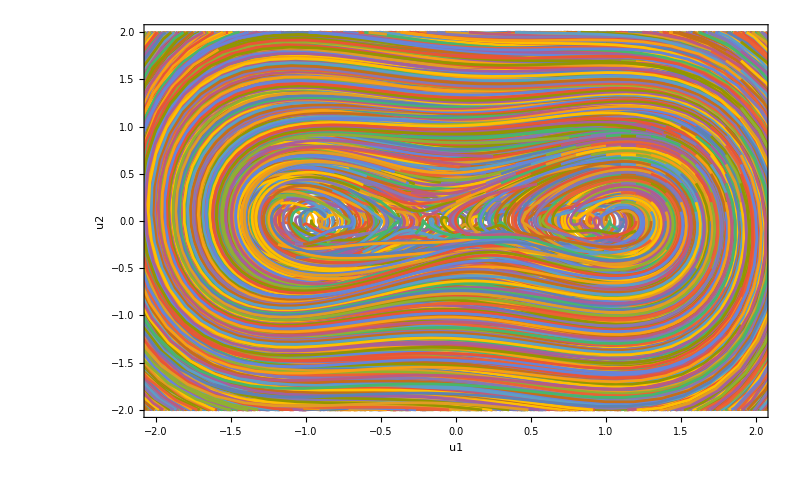

```mathematica
data3 = Import["FZ3", "Table"];
PlotFaze[data3]
```

```mathematica
(* Задача 16 варианта (Нелинейный осицллятор с несимметричной упругой характеристикой )*)
(*B = 0.16;
alpha = 0.05;
gamma = 0.5;
w = 0.833;
k = -0.5;
truesolve=DSolve[{y''[t]+alpha y'[t]+ k y[t] - B Cos[ w t]== 0, y[0] == 0.1, y'[0] == -0.1}, y[t], t][[1]][[1]][[2]]*)
```